## EdgesUsed-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51a (07 June 2017)) loaded Wed 7 Jun 2017 16:42:30
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

There are 8 cells in the tissue.

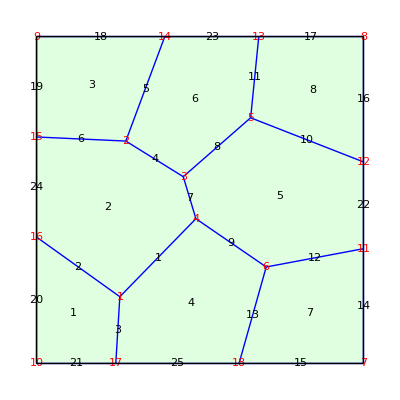

```mathematica
q=TemplateRandomSquareGrid[9, {-50, -50}, {50, 50}];
Q=Tissue2DTissue[q]; 
Print["There are ", NTissueCells[Q], " cells in the tissue."];  
ShowTissue[Q, "CellNumbers"-> True, Frame-> False, "EdgeStyles"-> Directive[Blue,Thick], "EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12]]
```

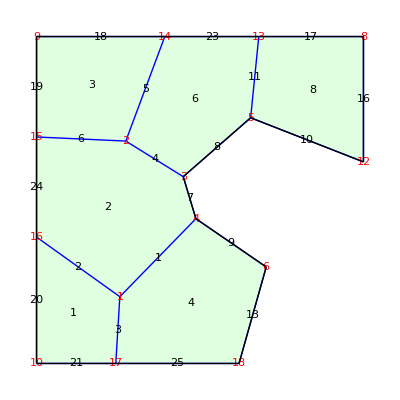

```mathematica
R=DeleteCell[Q, 5];
R=DeleteCell[R, 7];
ShowTissue[R, "CellNumbers"-> True, "EdgeStyles"-> Directive[Blue,Thick],"EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12]]
```

Now use the “All” option to show the edges and vertices that are NOT part of any cell

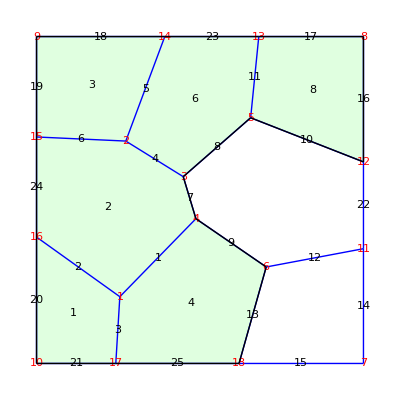

```mathematica
ShowTissue[R, "CellNumbers"-> True, "EdgeStyles"-> Directive[Blue,Thick],"EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12], 
"All"-> True]
```

```mathematica
R
```

DTissue[{{-24.5216,-29.5805},{-22.6954,18.0269},{-5.12052,7.13263},{-1.24829,-5.72333},{15.4914,25.1529},{20.2547,-20.4881},{50,-50},{50,50},{-50,50},{-50,-50},{50.,-14.8958},{50.,11.6506},{17.9817,50.},{-10.7673,50.},{-50.,19.2772},{-50.,-11.3388},{-25.7581,-50.},{11.94,-50.}},{{1,4},{1,16},{1,17},{2,3},{2,14},{2,15},{3,4},{3,5},{4,6},{5,12},{5,13},{6,11},{6,18},{7,11},{7,18},{8,12},{8,13},{9,14},{9,15},{10,16},{10,17},{11,12},{13,14},{15,16},{17,18}},{1→{21,3,2,20},2→{24,2,1,7,4,6},3→{19,6,5,18},4→{25,13,9,1,3},6→{23,5,4,8,11},8→{17,11,10,16}}]

```mathematica
TissueEdges[R]
```

{{1,4},{1,16},{1,17},{2,3},{2,14},{2,15},{3,4},{3,5},{4,6},{5,12},{5,13},{6,11},{6,18},{7,11},{7,18},{8,12},{8,13},{9,14},{9,15},{10,16},{10,17},{11,12},{13,14},{15,16},{17,18}}

Find the edges that are used:

```mathematica
EdgesUsed[R]
```

{1,2,3,4,5,6,7,8,9,10,11,13,16,17,18,19,20,21,23,24,25}

Find the edges that still exist in the tissue but are not used:

```mathematica
Complement[Range[NTissueEdges[R]], EdgesUsed[R]]
```

{12,14,15,22}

Find the vertices that are used

```mathematica
VerticesUsed[R]
```

{1,2,3,4,5,6,8,9,10,12,13,14,15,16,17,18}

Find the Vertices that remain in R that are not used:

```mathematica
Complement[Range[NTissueVertices[R]], VerticesUsed[R]]
```

{7,11}